This notebook generates plots for the Rail preprint. Enter the directory where “perform” files may be found below.

```mathematica
SetDirectory["/Users/eterna/results"];
```

```mathematica
(*Select samples*)
```

```mathematica
sampleNames={"NA19129_female_YRI_UU_6-1-1","NA07048_male_CEU_UU_6-1-2"}
```

{NA19129_female_YRI_UU_6-1-1,NA07048_male_CEU_UU_6-1-2}

```mathematica
(*Plot for female*)
```

```mathematica
allTrueStatsFiles=DeleteCases[(If[StringFreeQ[#, "withoutfilter"]&&!StringFreeQ[ #,"true"]&&!StringFreeQ[#,sampleNames[[1]]]&&StringFreeQ[#,"single"]&&(!StringFreeQ[#,"noann"]||!StringFreeQ[#,"rail"]||!StringFreeQ[#, "fromemr"]), #]&)/@FileNames["*"],Null]
```

{8core_NA19129_female_YRI_UU_6-1-1_hisat_noann_paired_1pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_hisat_noann_paired_2pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_rail_perform_true,8core_NA19129_female_YRI_UU_6-1-1_star_noann_paired_1pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_star_noann_paired_2pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_star_nogen_noann_paired_2pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_tophat_noann_paired_perform_true,fromemr_withfilter_NA19129_female_YRI_UU_6-1-1_perform_true}

```mathematica
allTrueStats = Import[#, "TSV"]&/@allTrueStatsFiles;
```

```mathematica
accumulated=Accumulate/@Transpose/@Transpose/@allTrueStats;
```

```mathematica
(*Plot of coverage bias correction vs. protocols using no annotation (Figure 5)*)
```

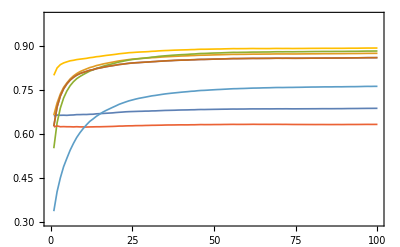

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->{All, {0.3, 1}}, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
allTrueStatsFilesAnn={"8core_NA19129_female_YRI_UU_6-1-1_hisat_ann_paired_1pass_perform_true","8core_NA19129_female_YRI_UU_6-1-1_star_ann_paired_1pass_perform_true",
"8core_NA19129_female_YRI_UU_6-1-1_tophat_ann_paired_perform_true",
"fromemr_withfilter_NA19129_female_YRI_UU_6-1-1_perform_true"}
```

{8core_NA19129_female_YRI_UU_6-1-1_hisat_ann_paired_1pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_star_ann_paired_1pass_perform_true,8core_NA19129_female_YRI_UU_6-1-1_tophat_ann_paired_perform_true,fromemr_withfilter_NA19129_female_YRI_UU_6-1-1_perform_true}

```mathematica
allTrueStats = Import[#, "TSV"]&/@allTrueStatsFilesAnn;
```

```mathematica
accumulated=Accumulate/@Transpose/@Transpose/@allTrueStats;
```

```mathematica
(*Plot of coverage bias correction vs. protocols using annotation (Figure 6)*)
```

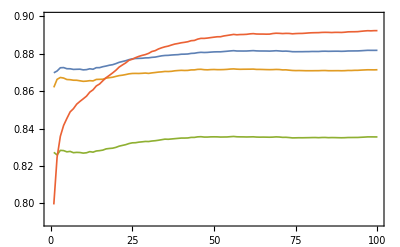

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->{{0, 100}, {0.79, 0.90}}, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
ListPlot[Table[N[#[[4]]]/#[[2]]&/@accumulated[[i]], {i, 1, Length[allTrueStats]}], Joined->True, PlotStyle->Thickness[.003], PlotRange->{All, {0.3, 1}}, Frame->True, FrameStyle->White,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Plot scaling with respect to number of samples (Figure 1c)*)
```

```mathematica
data={{28, 320/60}, {56, 495/60}, {112, 720/60}}
```

{{28,16/3},{56,33/4},{112,12}}

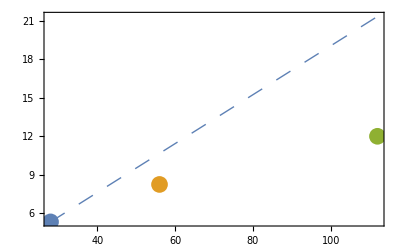

```mathematica
scaling=Show[ListPlot[data,PlotStyle->{White, Thick}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[1]], Point[data[[1]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[2]], Point[data[[2]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[3]], Point[data[[3]]]}],
ListPlot[{data[[1]], data[[1]]*2, data[[1]]*4}, Joined->True, PlotStyle->{ColorData[97,"ColorList"][[1]], Dashing[.03], Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```

```mathematica
(*Plot scaling with respect to number of instances (Figure 1a)*)
```

```mathematica
data={{10,28/(840/60)}, {20,28/(592/60)}, {40, 28/(320/60)}}//N
```

{{10.,2.},{20.,2.83784},{40.,5.25}}

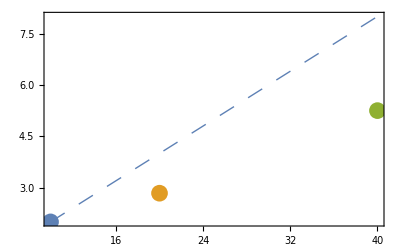

```mathematica
scaling=Show[ListPlot[data,PlotStyle->{White, Thick}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[1]], Point[data[[1]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[2]], Point[data[[2]]]}], Graphics[{PointSize[.03],ColorData[97,"ColorList"][[3]], Point[data[[3]]]}],
ListPlot[{data[[1]], data[[1]]*2, data[[1]]*4}, Joined->True, PlotStyle->{ColorData[97,"ColorList"][[1]], Dashing[.03], Thickness->0.0025}],
(*ParametricPlot[{data[[1]][[1]]x, data[[1]][[2]]Sqrt[x]}, {x, 1, 4}, PlotStyle->{Red, Dotted}],
ParametricPlot[{data[[2]][[1]]x, data[[2]][[2]]Sqrt[x]}, {x, 1, 2}, PlotStyle->{Green, Dotted}],*)
PlotRange->All, Frame->True, FrameStyle->Black,ImageSize->Full,BaseStyle->{FontName->"Arial", FontSize->30}, Background->None]
```